Reproducción de cuentas del paper de Bunkin “The New Concepts in the Optical Breakdown of Transparent Liquids”

2.1. Electron Avalanche Development inside the Bubstons

```mathematica
(*Defino parámetros*)
Subscript[R, 0] = 10^-6; (*Radio inicial del bubston en cm*)
Subscript[ν, ew]=; (*frecuencia de choque de un electrón con la pared del bubston*)
OverBar[Subscript[v, e]] =; (*velocidad media aritmética de los electrones*)
Subscript[ν, i]= ; (*frecuencia de ionización de las moléculas de la pared del bubston*)
Subscript[ℰ, e] =; (*energía del movimiento caótico de un electrón*)
OverDot[Subscript[ℰ, e]]=; (*average rate de incremento de la energía del movimiento caótico de un electrón*)
Subscript[ℰ, vib]=; (*average energía cinética de vibración de los electrones en un campo eléctrico con amplitud Subscript[E, 0] y frecuencia ω*)
Δ=;
e = ;
Subscript[Ε, 0]= ;
m =;
ω =;
Subscript[n, e cr]=;
c = ;
OverBar[Subscript[ℰ, e]] =; (**)
ℐ = c/(8 Pi)Subscript[Ε, 0]^2;
```

1000001/1000000

## Justificación de (1)

```mathematica
(*Eliminar todas las variables*)
Clear["Global`*"]
(*Identificar las variables con subíndice como variables*)
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

```mathematica
orden = 1;
```

Sea un electrón en el interior de un bubston, colisiona con la pared con una frecuencia ν_ew=OverBar[v_e] /R_0 e ioniza las moléculas de la pared con una frecuencia ν_i=OverDot[ℰ_e]/Δ. El aumento de su energía se debe a la presencia de un campo eléctrico de amplitud Ε_0 y frecuencia ω, es decir,

```mathematica
Ε[t_]:= Subscript[Ε, 0] Sin[ω t]
```

Sin colisiones, la ecuación de movimiento clásica es
m v̇ = q Ε(t)
donde q es la carga eléctrica
Teniendo en cuenta las colisiones con la pared como una fricción del electrón promedio,
m v̇ = q Ε(t) -m ν_ew v
Entonces,

```mathematica
(*uso la función Subscript[v, 1] para representar v*)
ClearAll[α,v,Subscript[ν, ew]]
solution=DSolve[{m α'[t]==-e Ε[t]-m Subscript[ν, ew] α[t],α[0]== (e Subscript[Ε, 0] ω)/(m (Subscript[ν, ew]^2+ω^2))},α[t],t];(*resuelvo la EDO*)
β[t_]=Simplify[α[t]/.solution[[1]]](*asigno a una función*)
```

(e Ε_0 (ω Cos[t ω]-ν_ew Sin[t ω]))/(m (ν_ew^2+ω^2))

* La condición inicial es tal que la solución obtenida ya es estacionaria. Si no se pusiera la solución sería una exponencial. A nosotros nos interesa el comportamiento estacionario, así que sacamos la dependencia exponencial. Si sacamos la exponencial a mano la solución deja de satisfacer β[0]=0

```mathematica
(*Tomamos el límite ω>>Subscript[ν, ew]. No sé hacerlo con Mathematica, lo hago a mano*)
 Subscript[ν, ew] = ϵ ω;
β[t_, ϵ_]=β[t]; (*Lo declaro como una función de ϵ*)
γ[t_, ϵ_]=Normal[Series[β[t, ϵ],{ϵ,0,orden}]]
```

(e Ε_0 Cos[t ω])/(m ω)-(e ϵ Ε_0 Sin[t ω])/(m ω)

```mathematica
(*Calculamos la potencia entregada*)
P[t,ϵ]=-e Ε[t] γ[t, ϵ];
(*Calculamos el promedio en un ciclo*)
T = (2 Pi)/ω;
Subscript[n, ciclos] = 0;
Subscript[t, min]= T*Subscript[n, ciclos];
Subscript[t, max] = T*(Subscript[n, ciclos]+1);
Print["Potencia media: "]
Integrate[P[t,Subscript[ν, ew]/ω],{t,Subscript[t, min],Subscript[t, max]}]/(Subscript[t, max]-Subscript[t, min])
```

Potencia media:

(e^2 ϵ Ε_0^2)/(2 m ω)

```mathematica
(*Veo si se cumple la relación entre potencia y Subscript[ℰ, vib]*)
OverBar[Subscript[ℰ, vib]]=Integrate[1/2 m γ[t,Subscript[ν, ew]/ω]^2,{t,Subscript[t, min],Subscript[t, max]}]/(Subscript[t, max]-Subscript[t, min]);
Print["Potencia media: "]
2 ϵ ω OverBar[Subscript[ℰ, vib]]
```

Potencia media:

(e^2 ϵ (1+ϵ^2) Ε_0^2)/(2 m ω)

A primer orden resultan ser las mismas expresiones
Defino como resultado de la cuenta la velocidad

```mathematica
ClearAll[Subscript[ν, ew]]
v[t_]:=γ[t, Subscript[ν, ew]/ω]
```

(e Ε_0 Cos[ω])/(m ω)-(e Ε_0 ν_ew Sin[ω])/(m ω^2)

donde ϵ = ν_ew/ ω

### Justificación de (1I)

```mathematica
Subscript[ω, a,e]=;
Subscript[N, e]=;
θ = ;

Subscript[ℐ, 0] = ;
Subscript[Δω, a,e]=;
𝒻=;
Subscript[T, e]=;
Q =;
Subscript[n, e]=;
OverBar[Subscript[n, e]]=;
Subscript[a, e]=;
```

### Justificación de 𝒻(ℰ_e)

ℰ_e es la energía del movimiento caótico de los electrones, es decir

```mathematica
Subscript[ℰ, e][t_] = 1/2 m v[t]^2
```

1/2 m ((e Ε_0 Cos[t ω])/(m ω)-(e Ε_0 ν_ew Sin[t ω])/(m ω^2))^2

Calculemos la derivada (d ℰ_e)/(d OverDot[ℰ_e])= (d ℰ_e)/dt(d t)/(d OverDot[ℰ_e])=(OverDot[ℰ_e]((d OverDot[ℰ_e])/dt))^-1

```mathematica
OverDot[Subscript[ℰ, e]][t_]=D[Subscript[ℰ, e][t],t];
dE2dt2[t_]=D[OverDot[Subscript[ℰ, e]][t],t]^-1
```

Set::write: Tag Power in 1/(m (-(e Ε_0 ν_ew Cos[Times[«2»]])/(m ω)-(e Ε_0 Sin[Times[«2»]])/m)^2+m (-(e Ε_0 ω Cos[t ω])/m+(e Ε_0 ν_ew Sin[t ω])/m) ((e Ε_0 Cos[t ω])/(m ω)-(e Ε_0 ν_ew Sin[t ω])/(m ω^2)))[t_] is Protected.

1/(m (-(e Ε_0 ν_ew Cos[t ω])/(m ω)-(e Ε_0 Sin[t ω])/m)^2+m (-(e Ε_0 ω Cos[t ω])/m+(e Ε_0 ν_ew Sin[t ω])/m) ((e Ε_0 Cos[t ω])/(m ω)-(e Ε_0 ν_ew Sin[t ω])/(m ω^2)))

1/(m (-(e Ε_0 ν_ew Cos[t ω])/(m ω)-(e Ε_0 Sin[t ω])/m)^2+m (-(e Ε_0 ω Cos[t ω])/m+(e Ε_0 ν_ew Sin[t ω])/m) ((e Ε_0 Cos[t ω])/(m ω)-(e Ε_0 ν_ew Sin[t ω])/(m ω^2)))[1]

```mathematica
factor[t_] = Simplify[OverDot[Subscript[ℰ, e]][t]dEdt2[t]]
```

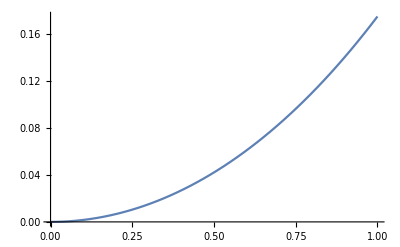

```mathematica
(*Grafico phi - eliminar*)
phi[r_]:=Sinh[r]/r-1
Plot[phi[r],{r,0,1}]
```

### Cuentas con los dedos

```mathematica
(*Eliminar todas las variables*)
Clear["Global`*"]
```

Creo que hacer las cuentas todas consistentes va a ser mucho trabajo, así que voy a ir haciendo cuentas una a una independiente de la anterior

```mathematica
(*Resuelvo ecuación diferencial aproximada para phi potencial*)
Simplify[DSolve[{1/r^2 D[r^2 D[phi[r],r],r]==α(1 +β phi[r] ),phi[0]==0},phi[r],r]]
```

{{phi[r]→(-ⅇ^(-r √α √β)+ⅇ^(r √α √β)-2 r √α √β)/(2 r √α β^(3/2))}}

```mathematica
(*Calculo el campo eléctrico*)
Clear["Global`*"]
Phi[r_]:=Subscript[T, e]/e(Sinh[r/a]/(r/a)-1)
Electrico[r_]:=-Simplify[D[Phi[r],r]]
Simplify[Electrico[r]^2/(8 Pi)]
```

((r Cosh[r/a]-a Sinh[r/a])^2 T_e^2)/(8 e^2 π r^4)

```mathematica
(*Defino la densidad y calculo el nro de electrones*)
Clear["Global`*"]
Subscript[n, e][r_]:=n0 Sinh[r/a]/(r/a)
4 Pi Integrate[r^2 Subscript[n, e][r],{r,0,R}]
```

Cosh[1]-Sinh[1]

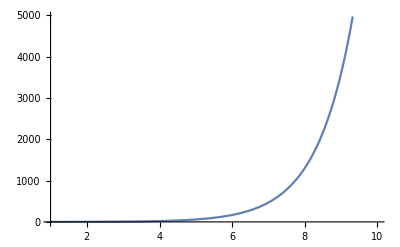

```mathematica
(*Grafico el nro de electrones*)
Clear["Global`*"]
Subscript[R, 0] = 1;
Ne[x_]:=(x Cosh[x]-Sinh[x])/x ;
Ne[1]
Plot[Ne[x],{x,1,10}]
```

```mathematica
(*Calculo la densidad media*)
```

```mathematica
Nelectrones[x_]:=[x Cosh[x]-Sinh[x]]/x 
Nelectrones[1]
```